### This is a function meant for testing the Transfer Integral at a single point in space. It requires the Overlap File(.txt), Coordinate File of the dimer(.xyz), the Molecular orbital file for each molecule in the calculation, the number of molecular orbitals, and the HOMO or LUMO

```mathematica
TransferCalc[overlapfile_,coordsfile_,orbitalfileA_,orbitalfileB_,numMOS_,HOMO_]:=
Module[{OverlapMatr,MOCoefftsA,MOCoefftsB,Transfer,foobarA,foobarB,j,homoA,homoB,foobarBnew},
OverlapMatr=FockOverlapUnravel[overlapfile,coordsfile,numMOS];
(*Print[OverlapMatr//MatrixForm];*)
MOCoefftsA=MOUnravel[orbitalfileA];
MOCoefftsB=MOUnravel[orbitalfileB];
foobarA=MOCoefftsA[[HOMO]];
foobarB=MOCoefftsB[[HOMO]];
(*foobarBnew=MORearrange[foobarB];*)
foobarBnew=foobarB;
homoA=Array[0&,{1,Length[foobarA]*2}];
homoB=Array[0&,{1,Length[foobarBnew]*2}];
Do[
homoA[[1]][[i]]=foobarA[[i]];
,{i,1,Length[foobarA]}
];

j=1;
Do[
homoB[[1]][[i]]=foobarBnew[[j]];
j = j+1;
,{i,Length[foobarBnew]+1,Length[foobarBnew]*2}
];
(*Print[homoB];*)
Transfer=homoA.OverlapMatr.Transpose[homoB];
Transfer=Abs[Transfer[[1]][[1]]];
Print[Transfer];
Transfer
];
```

```mathematica
TransferCalc["Thesis/Transfer/C2H4/BasisTest/Overlap/c2h42.txt","Thesis/Transfer/C2H4/631G/c2h4dimer.xyz","Thesis/Transfer/C2H4/BasisTest/c2h42.txt","Thesis/Transfer/C2H4/BasisTest/c2h42.txt",24,6]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

Part::partw: Part 395 of {"1", "2", "3", "4", "5", "1", "0.100000D+01", "2", "0.000000D+00", "0.100000D+01", "3", "0.000000D+00", "0.000000D+00", « 25 », "0.434923D+00", "0.000000D+00", "0.000000D+00", "-0.323896D+00", "0.000000D+00", "9", "0.125924D+00", "0.000000D+00", "0.665322D-01", "-0.137227D+00", "0.519440D+00", "10", « 344 »} does not exist.

0.0218947

0.0218947

#### AT EACH STEP I NEED TO CALCULATE NEW MOs for EACH MONOMER CAUSE THE NATURE OF THE INTERACTIONS IS CHANGING AS WE ROTATE!

```mathematica
Clear[OverlapMatr,Overlap,fock,Betavec]
```

```mathematica
Quiet[TransferCalc["Thesis/Transfer/C2H4/Overlaps/RotZ/c2h40test.txt","Thesis/Transfer/C2H4/RotZ/c2h40.xyz","Thesis/Transfer/C2H4/c2h4iso.txt","Thesis/Transfer/C2H4/c2h4iso.txt",24,6]]
```

(1. | 0. | 0. | 0. | 0.442573 | 0. | 0.436117 | 0. | 0.127581 | 0.127581 | 0.52171 | 0.52171 | 0.000332567 | 0.000515149 | 0. | 0. | 0.000213997 | 0.000321475 | 0.0000854387 | 0. | 0.000171111 | 0.000171111 | 0.000353963 | 0.000353963
0. | 1. | 0. | 0. | 0. | 0.274927 | 0. | 0. | 0. | 0. | 0. | 0. | -0.000515149 | -0.000804627 | 0. | 0. | -0.000321475 | -0.000484704 | -0.000138958 | 0. | -0.000235525 | -0.000235525 | -0.000509799 | -0.000509799
0. | 0. | 1. | 0. | -0.436117 | 0. | -0.323305 | 0. | -0.13884 | -0.13884 | 0.25781 | 0.25781 | 0. | 0. | 0.000062153 | 0. | -0.0000854387 | -0.000138958 | 1.21253×10^-6 | 0. | -0.0000894825 | -0.0000894825 | 0.0000581969 | 0.0000581969
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.274927 | 0.0674395 | -0.0674395 | 0.416772 | -0.416772 | 0. | 0. | 0. | 0.000062153 | 0. | 0. | 0. | 0.0000381434 | 0.0000434647 | -0.0000434647 | 0.0000940801 | -0.0000940801
0.442573 | 0. | -0.436117 | 0. | 1. | 0. | 0. | 0. | 0.52171 | 0.52171 | 0.127581 | 0.127581 | 0.000213997 | 0.000321475 | -0.0000854387 | 0. | 0.000332567 | 0.000515149 | 0. | 0. | 0.000353963 | 0.000353963 | 0.000171111 | 0.000171111
0. | 0.274927 | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000321475 | -0.000484704 | 0.000138958 | 0. | -0.000515149 | -0.000804627 | 0. | 0. | -0.000509799 | -0.000509799 | -0.000235525 | -0.000235525
0.436117 | 0. | -0.323305 | 0. | 0. | 0. | 1. | 0. | -0.25781 | -0.25781 | 0.13884 | 0.13884 | 0.0000854387 | 0.000138958 | 1.21253×10^-6 | 0. | 0. | 0. | 0.000062153 | 0. | -0.0000581969 | -0.0000581969 | 0.0000894825 | 0.0000894825
0. | 0. | 0. | 0.274927 | 0. | 0. | 0. | 1. | 0.416772 | -0.416772 | 0.0674395 | -0.0674395 | 0. | 0. | 0. | 0.0000381434 | 0. | 0. | 0. | 0.000062153 | 0.0000940801 | -0.0000940801 | 0.0000434647 | -0.0000434647
0.127581 | 0. | -0.13884 | 0.0674395 | 0.52171 | 0. | -0.25781 | 0.416772 | 1. | 0.167814 | 0.0629584 | 0.0223205 | 0.000171111 | 0.000235525 | -0.0000894825 | 0.0000434647 | 0.000353963 | 0.000509799 | -0.0000581969 | 0.0000940801 | 0.000561582 | 0.000276513 | 0.000160263 | 0.000081899
0.127581 | 0. | -0.13884 | -0.0674395 | 0.52171 | 0. | -0.25781 | -0.416772 | 0.167814 | 1. | 0.0223205 | 0.0629584 | 0.000171111 | 0.000235525 | -0.0000894825 | -0.0000434647 | 0.000353963 | 0.000509799 | -0.0000581969 | -0.0000940801 | 0.000276513 | 0.000561582 | 0.000081899 | 0.000160263
0.52171 | 0. | 0.25781 | 0.416772 | 0.127581 | 0. | 0.13884 | 0.0674395 | 0.0629584 | 0.0223205 | 1. | 0.167814 | 0.000353963 | 0.000509799 | 0.0000581969 | 0.0000940801 | 0.000171111 | 0.000235525 | 0.0000894825 | 0.0000434647 | 0.000160263 | 0.000081899 | 0.000561582 | 0.000276513
0.52171 | 0. | 0.25781 | -0.416772 | 0.127581 | 0. | 0.13884 | -0.0674395 | 0.0223205 | 0.0629584 | 0.167814 | 1. | 0.000353963 | 0.000509799 | 0.0000581969 | -0.0000940801 | 0.000171111 | 0.000235525 | 0.0000894825 | -0.0000434647 | 0.000081899 | 0.000160263 | 0.000276513 | 0.000561582
0.000332567 | -0.000515149 | 0. | 0. | 0.000213997 | -0.000321475 | 0.0000854387 | 0. | 0.000171111 | 0.000171111 | 0.000353963 | 0.000353963 | 1. | 0. | 0. | 0. | 0.442573 | 0. | 0.436117 | 0. | 0.127581 | 0.127581 | 0.52171 | 0.52171
0.000515149 | -0.000804627 | 0. | 0. | 0.000321475 | -0.000484704 | 0.000138958 | 0. | 0.000235525 | 0.000235525 | 0.000509799 | 0.000509799 | 0. | 1. | 0. | 0. | 0. | 0.274927 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.000062153 | 0. | -0.0000854387 | 0.000138958 | 1.21253×10^-6 | 0. | -0.0000894825 | -0.0000894825 | 0.0000581969 | 0.0000581969 | 0. | 0. | 1. | 0. | -0.436117 | 0. | -0.323305 | 0. | -0.13884 | -0.13884 | 0.25781 | 0.25781
0. | 0. | 0. | 0.000062153 | 0. | 0. | 0. | 0.0000381434 | 0.0000434647 | -0.0000434647 | 0.0000940801 | -0.0000940801 | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.274927 | 0.0674395 | -0.0674395 | 0.416772 | -0.416772
0.000213997 | -0.000321475 | -0.0000854387 | 0. | 0.000332567 | -0.000515149 | 0. | 0. | 0.000353963 | 0.000353963 | 0.000171111 | 0.000171111 | 0.442573 | 0. | -0.436117 | 0. | 1. | 0. | 0. | 0. | 0.52171 | 0.52171 | 0.127581 | 0.127581
0.000321475 | -0.000484704 | -0.000138958 | 0. | 0.000515149 | -0.000804627 | 0. | 0. | 0.000509799 | 0.000509799 | 0.000235525 | 0.000235525 | 0. | 0.274927 | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0.0000854387 | -0.000138958 | 1.21253×10^-6 | 0. | 0. | 0. | 0.000062153 | 0. | -0.0000581969 | -0.0000581969 | 0.0000894825 | 0.0000894825 | 0.436117 | 0. | -0.323305 | 0. | 0. | 0. | 1. | 0. | -0.25781 | -0.25781 | 0.13884 | 0.13884
0. | 0. | 0. | 0.0000381434 | 0. | 0. | 0. | 0.000062153 | 0.0000940801 | -0.0000940801 | 0.0000434647 | -0.0000434647 | 0. | 0. | 0. | 0.274927 | 0. | 0. | 0. | 1. | 0.416772 | -0.416772 | 0.0674395 | -0.0674395
0.000171111 | -0.000235525 | -0.0000894825 | 0.0000434647 | 0.000353963 | -0.000509799 | -0.0000581969 | 0.0000940801 | 0.000561582 | 0.000276513 | 0.000160263 | 0.000081899 | 0.127581 | 0. | -0.13884 | 0.0674395 | 0.52171 | 0. | -0.25781 | 0.416772 | 1. | 0.167814 | 0.0629584 | 0.0223205
0.000171111 | -0.000235525 | -0.0000894825 | -0.0000434647 | 0.000353963 | -0.000509799 | -0.0000581969 | -0.0000940801 | 0.000276513 | 0.000561582 | 0.000081899 | 0.000160263 | 0.127581 | 0. | -0.13884 | -0.0674395 | 0.52171 | 0. | -0.25781 | -0.416772 | 0.167814 | 1. | 0.0223205 | 0.0629584
0.000353963 | -0.000509799 | 0.0000581969 | 0.0000940801 | 0.000171111 | -0.000235525 | 0.0000894825 | 0.0000434647 | 0.000160263 | 0.000081899 | 0.000561582 | 0.000276513 | 0.52171 | 0. | 0.25781 | 0.416772 | 0.127581 | 0. | 0.13884 | 0.0674395 | 0.0629584 | 0.0223205 | 1. | 0.167814
0.000353963 | -0.000509799 | 0.0000581969 | -0.0000940801 | 0.000171111 | -0.000235525 | 0.0000894825 | -0.0000434647 | 0.000081899 | 0.000160263 | 0.000276513 | 0.000561582 | 0.52171 | 0. | 0.25781 | -0.416772 | 0.127581 | 0. | 0.13884 | -0.0674395 | 0.0223205 | 0.0629584 | 0.167814 | 1.)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13 | -13 | -13 | -13 | -13 | -13 | -13 | -13 | -9 | -9 | -9 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13 | -13 | -13 | -13 | -13 | -13 | -13 | -13 | -9 | -9 | -9 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13 | -13 | -13 | -13 | -13 | -13 | -13 | -13 | -9 | -9 | -9 | -9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -13 | -13 | -13 | -13 | -13 | -13 | -13 | -13 | -9 | -9 | -9 | -9
-17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-17 | -17 | -17 | -17 | -17 | -17 | -17 | -17 | -13 | -13 | -13 | -13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-13 | -13 | -13 | -13 | -13 | -13 | -13 | -13 | -9 | -9 | -9 | -9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-13 | -13 | -13 | -13 | -13 | -13 | -13 | -13 | -9 | -9 | -9 | -9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-13 | -13 | -13 | -13 | -13 | -13 | -13 | -13 | -9 | -9 | -9 | -9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-13 | -13 | -13 | -13 | -13 | -13 | -13 | -13 | -9 | -9 | -9 | -9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00565364 | -0.00875753 | 0. | 0. | -0.00363795 | -0.00546508 | -0.00145246 | 0. | -0.00222444 | -0.00222444 | -0.00460152 | -0.00460152
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00875753 | 0.0136787 | 0. | 0. | 0.00546508 | 0.00823997 | 0.00236229 | 0. | 0.00306183 | 0.00306183 | 0.00662739 | 0.00662739
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0010566 | 0. | 0.00145246 | 0.00236229 | -0.000020613 | 0. | 0.00116327 | 0.00116327 | -0.00075656 | -0.00075656
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0010566 | 0. | 0. | 0. | -0.000648438 | -0.000565041 | 0.000565041 | -0.00122304 | 0.00122304
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00363795 | -0.00546508 | 0.00145246 | 0. | -0.00565364 | -0.00875753 | 0. | 0. | -0.00460152 | -0.00460152 | -0.00222444 | -0.00222444
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00546508 | 0.00823997 | -0.00236229 | 0. | 0.00875753 | 0.0136787 | 0. | 0. | 0.00662739 | 0.00662739 | 0.00306183 | 0.00306183
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00145246 | -0.00236229 | -0.000020613 | 0. | 0. | 0. | -0.0010566 | 0. | 0.00075656 | 0.00075656 | -0.00116327 | -0.00116327
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.000648438 | 0. | 0. | 0. | -0.0010566 | -0.00122304 | 0.00122304 | -0.000565041 | 0.000565041
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00222444 | -0.00306183 | 0.00116327 | -0.000565041 | -0.00460152 | -0.00662739 | 0.00075656 | -0.00122304 | -0.00505424 | -0.00248862 | -0.00144237 | -0.000737091
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00222444 | -0.00306183 | 0.00116327 | 0.000565041 | -0.00460152 | -0.00662739 | 0.00075656 | 0.00122304 | -0.00248862 | -0.00505424 | -0.000737091 | -0.00144237
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00460152 | -0.00662739 | -0.00075656 | -0.00122304 | -0.00222444 | -0.00306183 | -0.00116327 | -0.000565041 | -0.00144237 | -0.000737091 | -0.00505424 | -0.00248862
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00460152 | -0.00662739 | -0.00075656 | 0.00122304 | -0.00222444 | -0.00306183 | -0.00116327 | 0.000565041 | -0.000737091 | -0.00144237 | -0.00248862 | -0.00505424
-0.00565364 | 0.00875753 | 0. | 0. | -0.00363795 | 0.00546508 | -0.00145246 | 0. | -0.00222444 | -0.00222444 | -0.00460152 | -0.00460152 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00875753 | 0.0136787 | 0. | 0. | -0.00546508 | 0.00823997 | -0.00236229 | 0. | -0.00306183 | -0.00306183 | -0.00662739 | -0.00662739 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.0010566 | 0. | 0.00145246 | -0.00236229 | -0.000020613 | 0. | 0.00116327 | 0.00116327 | -0.00075656 | -0.00075656 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.0010566 | 0. | 0. | 0. | -0.000648438 | -0.000565041 | 0.000565041 | -0.00122304 | 0.00122304 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00363795 | 0.00546508 | 0.00145246 | 0. | -0.00565364 | 0.00875753 | 0. | 0. | -0.00460152 | -0.00460152 | -0.00222444 | -0.00222444 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00546508 | 0.00823997 | 0.00236229 | 0. | -0.00875753 | 0.0136787 | 0. | 0. | -0.00662739 | -0.00662739 | -0.00306183 | -0.00306183 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00145246 | 0.00236229 | -0.000020613 | 0. | 0. | 0. | -0.0010566 | 0. | 0.00075656 | 0.00075656 | -0.00116327 | -0.00116327 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.000648438 | 0. | 0. | 0. | -0.0010566 | -0.00122304 | 0.00122304 | -0.000565041 | 0.000565041 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00222444 | 0.00306183 | 0.00116327 | -0.000565041 | -0.00460152 | 0.00662739 | 0.00075656 | -0.00122304 | -0.00505424 | -0.00248862 | -0.00144237 | -0.000737091 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00222444 | 0.00306183 | 0.00116327 | 0.000565041 | -0.00460152 | 0.00662739 | 0.00075656 | 0.00122304 | -0.00248862 | -0.00505424 | -0.000737091 | -0.00144237 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00460152 | 0.00662739 | -0.00075656 | -0.00122304 | -0.00222444 | 0.00306183 | -0.00116327 | -0.000565041 | -0.00144237 | -0.000737091 | -0.00505424 | -0.00248862 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00460152 | 0.00662739 | -0.00075656 | 0.00122304 | -0.00222444 | 0.00306183 | -0.00116327 | 0.000565041 | -0.000737091 | -0.00144237 | -0.00248862 | -0.00505424 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

0.0219186

```mathematica
TransferTestTrans[orbitalfileA_,coordsfile_,overlappath_,orbitalpath_,numMOS_,HOMO_]:=
Module[{Calc,overlapfile,num,ext,file,CalcList,RotList,Riffled,Partitioned,plot2,orbitalfileB},
CalcList={};
Do[
num=ToString[i];
ext=".txt";
overlapfile=overlappath<>num<>ext;
orbitalfileB=orbitalpath<>num<>"iso"<>ext;
Calc=Quiet[TransferCalc[overlapfile,coordsfile,orbitalfileA,orbitalfileB,numMOS,HOMO]];
CalcList=Append[CalcList,Calc];
,{i,0,14}];
RotList={0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7};
Riffled=Riffle[RotList,CalcList];
Partitioned=Partition[Riffled,2];
ListPlot[{Partitioned},Joined->False]

];
```

```mathematica
p=TransferTestTrans["Thesis/Transfer/Pentacene/TransX/pentacene0iso.txt","Thesis/Transfer/Pentacene/pentacenedimer.xyz","Thesis/Transfer/Pentacene/TransX/Overlaps/pentacene","Thesis/Transfer/Pentacene/TransX/pentacene",204,51];
```

0.31156

0.265452

0.14305

0.0151314

0.159298

0.245757

0.252188

0.184586

0.0714685

0.0482424

0.137776

0.174968

0.157739

0.100684

0.0273385

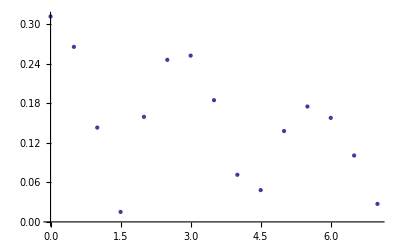

```mathematica
p
```

```mathematica
TransferTestRot[orbitalfileA_,coordsfile_,overlappath_,orbitalpath_,numMOS_,HOMO_]:=
Module[{Calc,overlapfile,num,ext,file,CalcList,RotList,Riffled,Partitioned,orbitalfileB},
CalcList={};
Do[
num=ToString[i];
ext=".txt";
overlapfile=overlappath<>num<>ext;
orbitalfileB=orbitalpath<>num<>"iso"<>ext;
Calc=Quiet[TransferCalc[overlapfile,coordsfile,orbitalfileA,orbitalfileB,numMOS,HOMO]];
CalcList=Append[CalcList,Calc];
,{i,0,18}];
RotList={0,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180};
Riffled=Riffle[RotList,CalcList];
Partitioned=Partition[Riffled,2];
ListPlot[{Partitioned},Joined->False]
];
```

0.0219186

0.0215856

0.0205968

0.0189821

0.0167906

0.014089

0.0109593

0.00749661

0.00380612

2.58277×10^-18

0.00380612

0.00749661

0.0109593

0.014089

0.0167906

0.0189821

0.0205968

0.0215856

0.0219186

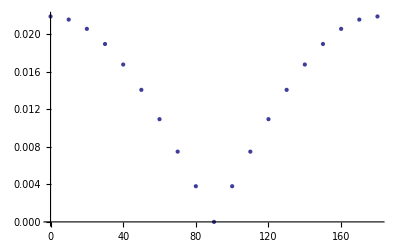

```mathematica
TransferTestRot["Thesis/Transfer/C2H4/RotZ/c2h40iso.txt","Thesis/Transfer/C2H4/c2h4dimer.xyz","Thesis/Transfer/C2H4/Overlaps/RotZ/c2h4","Thesis/Transfer/C2H4/RotZ/c2h4",24,6]
```